# Bosonic Complexity of Purification (BCoP)

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

First step: Import the GaussianOptimization Package (Run):

```mathematica
Import["/Users/HugoCamargo89/Desktop/gaussian_purifications/Mathematica Code/GaussianOptimization.m"]
```

```mathematica
(*<<GaussianOptimization`*)
```

In this Mathematica notebook we use the optimization procedure to find the complexity of purification for three bosonic systems. The first system is a lattice free scalar field theory with periodic conditions (this Chapter is called Bosons on a Periodic Lattice - Vacuum State), the second one is a thermal state in a lattice scalar field theory (this Chapter is called Thermal States on a Periodic Lattice), and the third one is for the time-dependent thermofield double state.

## Bosons on a Periodic Lattice - Vacuum State

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for the vacuum state of a bosonic system on a periodic lattice. The SubChapter: FT Definitions NEW (Run), should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

FT Definitions NEW (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystem partitions: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NNδ . (!  Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN(! Counting starts at site 0 !)
10. Reference State Frequency: μ

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) KGft[{NN,δ,m,μ}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGcmRes[NNδmμ,{dimA,dimB,d}].

Notice: In order to account for a non-unit reference state frequency, we simply divide ω by μ in the following:

```mathematica
KGft[{NN_,δ_,m_,μ_}]:=KGft[{NN,δ,m,μ}]={Fourier[Table[(√((m^2+(2/δ Sin[(π k)/NN])^2)/NN))/μ,{k,0,NN-1}]]//Re,Fourier[Table[μ/√(NN(m^2+(2/δ Sin[(π k)/NN])^2)),{k,0,NN-1}]]//Re};
KGb[var_]:=KGb[var]={ToeplitzMatrix[KGft[var]⟦1⟧],ToeplitzMatrix[KGft[var]⟦2⟧]};
KGcm[var_]:=KGcm[var]=ArrayFlatten[{{KGb[var]⟦1⟧,0.},{0.,KGb[var]⟦2⟧}}];(* in qqpp basis *)
KGcmRes[NNδmμ_,{dimA_,dimB_,d_}]:=KGcmRes[NNδmμ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGb[NNδmμ]⟦1,ind,ind⟧,0.},{0.,KGb[NNδmμ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

Notice: KGcm is in a “qqpp” basis. In order to transform to a “qpqp” basis, simply multiply by GOqpqpFROMqqpp[NN], as in the following example:

#### Check how to get G in “qpqp” basis

```mathematica
GOqpqpFROMqqpp[2].KGcm[{2,1,1/10,1}].Transpose[GOqpqpFROMqqpp[2]]//MatrixForm
```

(1.05125 | 0. | -0.951249 | 0.
0. | 5.24969 | 0. | 4.75031
-0.951249 | 0. | 1.05125 | 0.
0. | 4.75031 | 0. | 5.24969)

```mathematica
KGcmRes[{2,1,1/10,1},{1,0,0}]//MatrixForm
```

(1.05125 | 0.
0. | 5.24969)

## Bosonic Complexity of Purification (CoP) for Vacuum State as a Function of Subsystem/Total System Size Ratio

### Definition of System Parameters

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystems: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NNδ . (! Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN (! Counting starts at site 0 !)

NN =; (* number of lattice sites *)
δ =; (* lattice spacing *)
m =; (* mass *)
dimA1 =; (* # dofs in subsystem A1 *)
dimB1 =; (* # dofs in subsystem B1 *)
d =; (* lattice distance between subsystem partitions A1 and B1 *)
dimPur = dimA1 + dimB1; (* dimensions of the purifying system - In this case, minimal purification*)
μ =; (*Reference state frequency*)
L = NN δ ; (*Total length of the circle*)
l = (dimA1 + dimB1) δ ;(*Length of the subsystem*)
r = l/L; (*Ratio of subsystem/sistem size l/L=(dimA1+dimB1)/NN*)

#### a). Setting the System Parameters

```mathematica
L=10;
δ=1/10;
m=1/10;
NN=L/δ;
μ=1;
(*r=l/L; Ratio of subsystem/sistem size - Goes from 0 to 1*)
dimB1=0;
d=0;
(*dimPur=dimA1+dimB1;*)
(*dimA1= r NN;*)
```

```mathematica
(*{{NN,δ,m,μ},{dimA1,dimB1,d}}*)
```

```mathematica
(*{{L/δ,δ,m,μ},{(r L)/δ,dimB1,d}}*)
```

```mathematica
ArrayRatiolist=Table[{4i /NN},{i,1,NN/4}]; (*List of ratio values*)
Ratiolist=Flatten[ArrayRatiolist];
dimA1= NN Ratiolist; (*List of subsystem Size*) 
dimPur=dimA1; (*Minimal Purification - dimB1=0*)
```

```mathematica
dimA1
Ratiolist
dimPur
```

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100}

{1/25,2/25,3/25,4/25,1/5,6/25,7/25,8/25,9/25,2/5,11/25,12/25,13/25,14/25,3/5,16/25,17/25,18/25,19/25,4/5,21/25,22/25,23/25,24/25,1}

{4,8,12,16,20,24,28,32,36,40,44,48,52,56,60,64,68,72,76,80,84,88,92,96,100}

#### b). Initial Mixed State Covariance Matrix

```mathematica
TableCM0=Table[KGcmRes[{NN,δ,m,μ},{dimA1⟦i⟧,dimB1,d}],{i,1,Length[Ratiolist]}];
```

#### c). Purified State Complex Structure

```mathematica
rlist=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[Ratiolist]}]⟦All,1⟧;
MTra=Table[Table[GOExtractStdFormG[TableCM0⟦i⟧],{i,1,Length[TableCM0]}]⟦j⟧,{j,1,Length[Ratiolist]}]⟦All,2⟧;
```

```mathematica
JT=Table[GOPurifyStandardJBoson[rlist⟦i⟧,dimPur⟦i⟧,"qpqp"],{i,Length[Ratiolist]}];
JR0=Table[GOTransformGtoJ[IdentityMatrix[2(dimA1⟦i⟧+dimPur⟦i⟧)],"qpqp","qpqp"],{i,Length[Ratiolist]}]; (*Notice missing dimB1 in the previous formula - because we set it to 0*)
```

#### d). Problem-Specific Input

```mathematica
function=Table[GOCoPBos[JT⟦i⟧],{i,Length[Ratiolist]}]; 
gradient=Table[GOCoPgradBos[JT⟦i⟧],{i,Length[Ratiolist]}];
```

```mathematica
ProblemSpecific=Table[{function⟦i⟧,gradient⟦i⟧},{i,Length[Ratiolist]}];
```

#### e). System-Specific Input

```mathematica
LieBasis=Table[GOLieBasisCompound[{GOLieBasisEmpty[dimA1⟦i⟧],GOLieBasisSpNoUN[dimPur⟦i⟧]}],{i,Length[Ratiolist]}];
```

```mathematica
Length[LieBasis]
Dimensions[LieBasis]
```

25

{25}

```mathematica
Table[Dimensions[LieBasis⟦i⟧],{i,Length[LieBasis]}]
```

{{20,16,16},{72,32,32},{156,48,48},{272,64,64},{420,80,80},{600,96,96},{812,112,112},{1056,128,128},{1332,144,144},{1640,160,160},{1980,176,176},{2352,192,192},{2756,208,208},{3192,224,224},{3660,240,240},{4160,256,256},{4692,272,272},{5256,288,288},{5852,304,304},{6480,320,320},{7140,336,336},{7832,352,352},{8556,368,368},{9312,384,384},{10100,400,400}}

```mathematica
(*Looks like calculating 10k matrices of 400x400 can take a lot of time.*)
```

```mathematica
(*Input arrangement useful for non-minimal purifications*)
```

```mathematica
M0=Table[ArrayFlatten[{{MTra⟦i⟧,0},{0,IdentityMatrix[2dimPur⟦i⟧]}}]//SparseArray,{i,Length[Ratiolist]}];
```

```mathematica
(* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

```mathematica
Length[M0]
Dimensions[M0]
```

25

{25}

```mathematica
MatrixExp[RandomReal[{0,7/10},Length[LieBasis⟦1⟧]].LieBasis⟦1⟧]//MatrixForm
```

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.63057 | 0.476686 | 0.43772 | 0.410767 | 0.194009 | 0.0695274 | 0.717762 | 0.281683
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.476686 | 1.01272 | 0.441243 | 0.195024 | 0.249211 | 0.0071575 | 0.428396 | -0.266921
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.43772 | 0.441243 | 1.63663 | 0.630576 | 0.708786 | -0.00454652 | 0.732211 | 0.197626
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.410767 | 0.195024 | 0.630576 | 1.224 | 0.23575 | -0.307398 | 0.406737 | -0.29027
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.194009 | 0.249211 | 0.708786 | 0.23575 | 1.71084 | 0.0217242 | 0.288237 | 0.0975335
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0695274 | 0.0071575 | -0.00454652 | -0.307398 | 0.0217242 | 0.716643 | 0.0307611 | 0.0352473
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.717762 | 0.428396 | 0.732211 | 0.406737 | 0.288237 | 0.0307611 | 1.40552 | 0.24567
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.281683 | -0.266921 | 0.197626 | -0.29027 | 0.0975335 | 0.0352473 | 0.24567 | 1.1799)

```mathematica
M0List=Table[Table[MatrixExp[RandomReal[{0,1/10},Length[LieBasis⟦j⟧]].LieBasis⟦j⟧].M0⟦j⟧,{i,1}],{j,Length[Ratiolist]}];
```

```mathematica
(*Here we have only one M0 per case. More random initial matrices M0 could be generated.*)
```

```mathematica
(*M0List=Table[Table[MatrixExp[RandomReal[{0,7/10},Length[LieBasis⟦i⟧]].LieBasis⟦i⟧].M0⟦j⟧,{i,10}],{j,Length[Ratiolist]}];*)(*Here we generate 10 initial points.*)
```

```mathematica
Length[M0List]
Dimensions[M0List]
Dimensions[M0List⟦1⟧⟦1⟧]
```

25

{25,1}

{16,16}

```mathematica
M0List⟦1⟧⟦1⟧//MatrixForm
```

(0.0686483 | 1.10849 | 0.0668313 | 0.474437 | 0.0668313 | 0.474437 | 0.0686483 | 1.10849 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.302835 | 0.251278 | -0.29482 | 0.107548 | -0.29482 | 0.107548 | -0.302835 | 0.251278 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.203633 | -0.527033 | 0.0609453 | -0.0735466 | -0.0609453 | 0.0735466 | -0.203633 | 0.527033 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.0480711 | 2.23255 | 0.0143872 | 0.311548 | -0.0143872 | -0.311548 | -0.0480711 | -2.23255 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.00531767 | 1.88257 | -0.0124244 | -1.93375 | -0.0124244 | -1.93375 | 0.00531767 | 1.88257 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0777534 | 0.128752 | 0.181665 | -0.132252 | 0.181665 | -0.132252 | -0.0777534 | 0.128752 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0231429 | -0.00583163 | 0.165841 | 0.0194848 | -0.165841 | -0.0194848 | 0.0231429 | 0.00583163 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.000155821 | -0.866125 | -0.00111661 | 2.89393 | 0.00111661 | -2.89393 | -0.000155821 | 0.866125 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.05979 | 0.0783007 | 0.00445994 | 0.0587713 | 0.0267301 | 0.0257755 | 0.0623492 | 0.0156287
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0783007 | 0.956413 | 0.0535274 | 0.0037106 | 0.024412 | -0.0129382 | 0.0189386 | -0.0491506
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.00445994 | 0.0535274 | 1.02666 | 0.0128613 | 0.0108234 | 0.0453528 | 0.0194135 | 0.0524874
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0587713 | 0.0037106 | 0.0128613 | 0.982758 | 0.0518389 | 0.000199691 | 0.0590189 | -0.0113002
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0267301 | 0.024412 | 0.0108234 | 0.0518389 | 1.11045 | 0.0797801 | 0.0678594 | 0.0669909
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0257755 | -0.0129382 | 0.0453528 | 0.000199691 | 0.0797801 | 0.916267 | 0.067721 | -0.0478369
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0623492 | 0.0189386 | 0.0194135 | 0.0590189 | 0.0678594 | 0.067721 | 1.05563 | 0.0340951
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.0156287 | -0.0491506 | 0.0524874 | -0.0113002 | 0.0669909 | -0.0478369 | 0.0340951 | 0.962103)

```mathematica
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
(*Previous input: metric=GOMetricSp[LieBasis,JR0];*)
(*geometry=Table[GOGeometryConst[LieBasis⟦i⟧,JR0⟦i⟧,+1],{i,Length[Ratiolist]}];*)(*$Aborted*)(*Takes ∞ time to compute! Calculating pseudo-inverse is hard!*)
```

```mathematica
Monitor[Table[Geometry[i]=GOGeometryConst[LieBasis⟦i⟧,JR0⟦i⟧,+1],{i,Length[Ratiolist]}],i];
```

```mathematica
(*metric=GOMetricSp[LieBasis,JR0]*)
```

```mathematica
geometry=Table[Geometry[i],{i,Length[Ratiolist]}];
```

```mathematica
SystemSpecific=Table[{JR0⟦i⟧,M0List⟦i⟧,LieBasis⟦i⟧,geometry⟦i⟧,newM},{i,Length[Ratiolist]}];
```

```mathematica
Length[SystemSpecific]
Dimensions[SystemSpecific]
Dimensions[SystemSpecific⟦1⟧]
```

25

{25,5}

{5}

#### f). Procedure-Specific Input

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-10; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 10 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

#### g). Optimization

```mathematica
Monitor[Table[Timing[Optimize[j]=GOOptimize[ProblemSpecific⟦j⟧,SystemSpecific⟦j⟧,ProcedureSpecific]],{j,1,Length[Ratiolist]}],j]
```

```mathematica
Time=Table[Optimize[j],{j,Length[Ratiolist]}]⟦All,1⟧;
```

```mathematica
Result=Table[Optimize[j],{j,Length[Ratiolist]}]⟦All,2⟧;
```

```mathematica
Dimensions[Time]
```

{32}

```mathematica
Dimensions[Result]
Dimensions[Result⟦1⟧]
```

{32,6}

{6}

#### h). Results

```mathematica
Print["Time taken: ",Time," seconds"];
```

Time taken: {1587.3,1595.94,1609.95,1743.94,1859.32,1358.44,1403.34,729.915,1555.55,1698.11,2138.27,783.65,752.151,1007.77,1011.53,882.011,668.374,627.712,972.128,1296.01,4034.56,4414.41,3762.07,3829.74,3481.46,2101.53,1788.6,1245.22,1485.76,1513.97,1486.23,2316.66} seconds

```mathematica
Print["Total Time taken: ",Total[Time/60]/60," hours"];
```

Total Time taken: 15.7616 hours

```mathematica
Print["Final values: ",Table[Result⟦i⟧⟦1,1⟧,{i,Length[Result]}]];
```

Final values: {1.73843,1.77167,1.7834,1.7901,1.79439,1.7973,1.79934,1.80081,1.80188,1.80268,1.80328,1.80374,1.80408,1.80472,1.80513,1.8053,1.80532,1.8053,1.80513,1.80471,1.80373,1.80328,1.80268,1.80188,1.8008,1.79933,1.7973,1.7944,1.79013,1.78351,1.77202,1.74032}

```mathematica
Print["Number of iterations: ",Table[Length[Result⟦i⟧⟦4,1⟧],{i,Length[Result]}]];
```

Number of iterations: {6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,7,7,6,6}

```mathematica
Print["Number of total corrections: ",Table[Result⟦i⟧⟦3⟧//Total,{i,Length[Result]}]];
```

Number of total corrections: {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

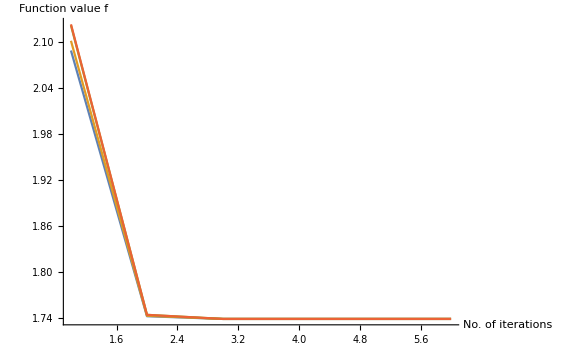
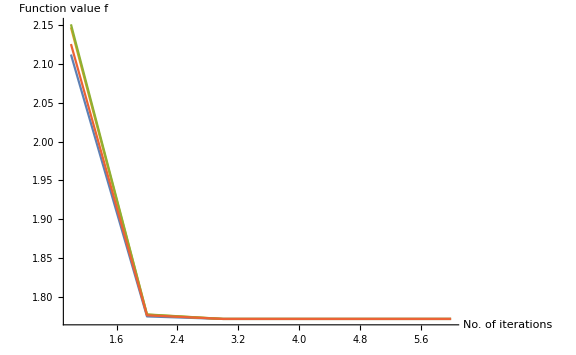
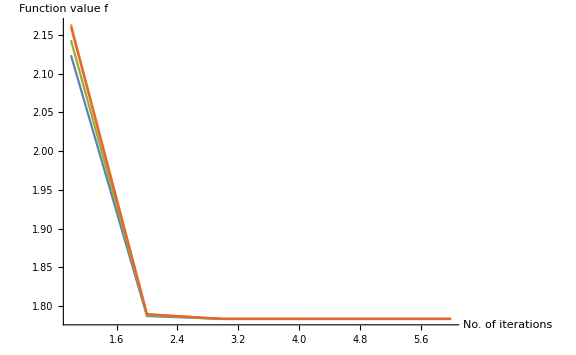
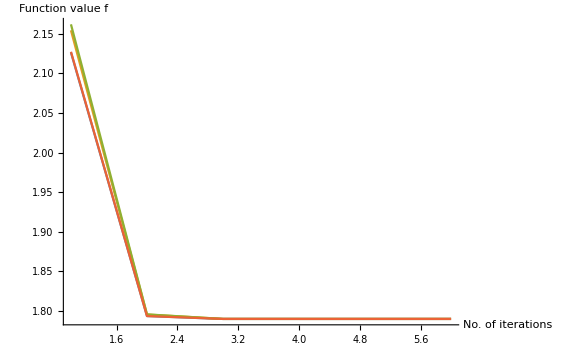
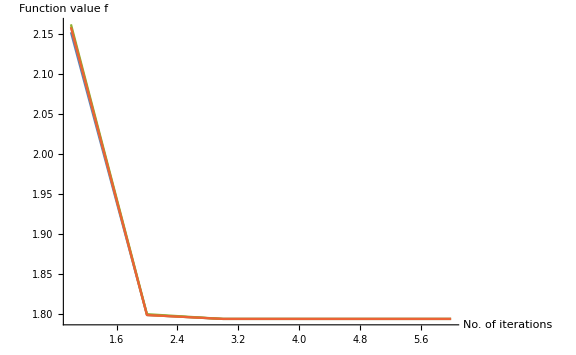
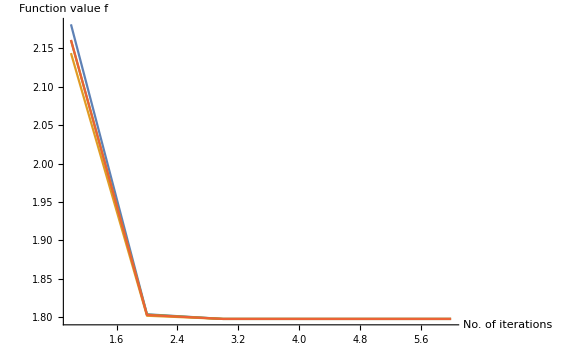
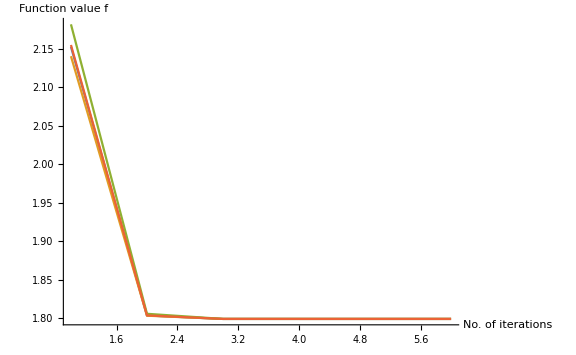
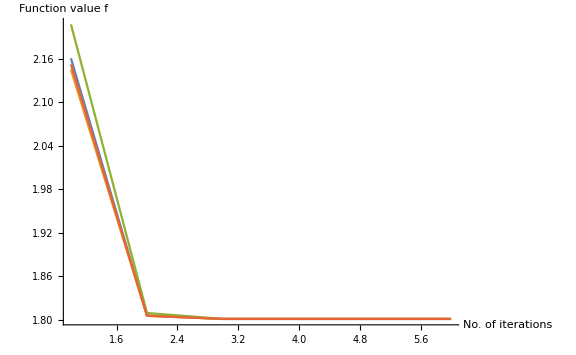

```mathematica
Table[ListPlot[Result⟦i⟧⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True],{i,Length[Result]}]
```

```mathematica
(*Expand the previous entry to view the convergence for the individual points in the optimization.*)
```

```mathematica
ListSubCase15new=Join[Arrayseplist,Table[Result⟦i,1⟧,{i,Length[seplist]}],2]
Export[NotebookDirectory[]<>"ListBCoPdimA110B110.txt",ListSubCase15new];
```

{{0,1.73843},{1,1.77167},{2,1.7834},{3,1.7901},{4,1.79439},{5,1.7973},{6,1.79934},{7,1.80081},{8,1.80188},{9,1.80268},{10,1.80328},{11,1.80374},{12,1.80408},{15,1.80472},{20,1.80513},{30,1.8053},{40,1.80532},{50,1.8053},{60,1.80513},{65,1.80471},{69,1.80373},{70,1.80328},{71,1.80268},{72,1.80188},{73,1.8008},{74,1.79933},{75,1.7973},{76,1.7944},{77,1.79013},{78,1.78351},{79,1.77202},{80,1.74032}}

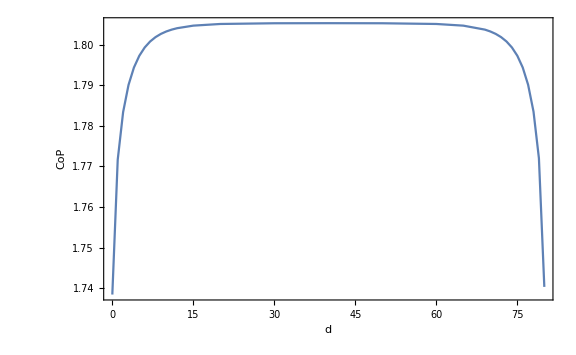

```mathematica
ListPlot[ListSubCase15new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

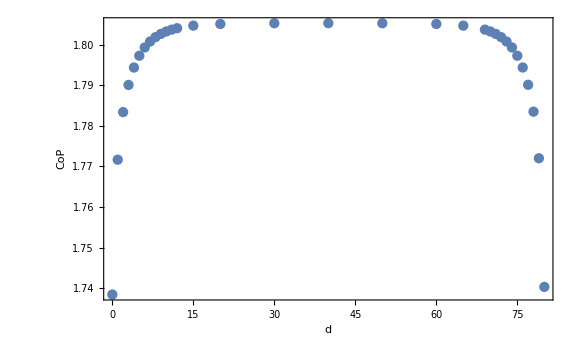
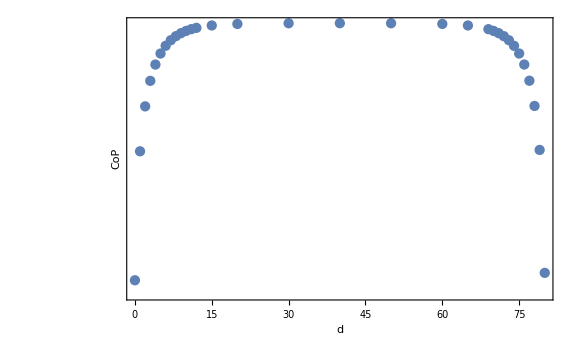
-Graphics--Graphics--Graphics-

```mathematica
PlotListSubCase15new=Row[{ListPlot[ListSubCase15new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListPlot[ListSubCase15new,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[ListSubCase15new,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotListBCoPdimA110B110.pdf",PlotListSubCase15new];
```

## Thermal States on a Periodic Lattice

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for a thermal state on a circle. The SubChapter: Definitions (Run), should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

Definitions (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Inverse Temperature: β,
3. Mass of the Scalar Field: m,
4. Lattice Spacing: δ,
5. Dimension of subsystems on the lattice: dimA1 & dimB1,
6. Lattice Site Separation between the subsystems: d,
7. Dimension of purifications: dimPur
8. Total length of the circle: L==NN δ . (! Counting starts at site 0 !)
9. Length of the subsystem: l=(dimA1+dimB1)δ
10. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1/NN (! Counting starts at site 0 !)

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) KGThft[{NN,δ,m,β}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGThcmRes[NNδmβ,{dimA,dimB,d}].

```mathematica
ω[NN_,δ_,m_,k_]:=√(m^2+(2/δ Sin[(π k)/NN])^2);
```

```mathematica
α[NN_,δ_,m_,k_,β_]:=1/2 Log[Coth[(β ω[NN,δ,m,k])/4]];
```

Notice that input for KGThft is a list: {NN,δ,m,β}:

```mathematica
KGThft[{NN_,δ_,m_,β_}]:=KGThft[{NN,δ,m,β}]={Fourier[Table[Cosh[2α[NN,δ,m,k,β]] ω[NN,δ,m,k]/(√NN),{k,0,NN-1}]]//Re,Fourier[Table[(Cosh[2α[NN,δ,m,k,β]]/(√NN ω[NN,δ,m,k])),{k,0,NN-1}]]//Re};
KGThb[var_]:=KGThb[var]={ToeplitzMatrix[KGThft[var]⟦1⟧],ToeplitzMatrix[KGThft[var]⟦2⟧]};
KGThcm[var_]:=KGThcm[var]=ArrayFlatten[{{KGThb[var]⟦1⟧,0.},{0.,KGThb[var]⟦2⟧}}];(* in qqpp basis *)
KGThcmRes[NNδmβ_,{dimA_,dimB_,d_}]:=KGThcmRes[NNδmβ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGThb[NNδmβ]⟦1,ind,ind⟧,0.},{0.,KGThb[NNδmβ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

```mathematica
KGcm[{10,1/10,1/10}]//MatrixForm
```

(12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724)

```mathematica
KGThcm[{10,1/10,1/10,1000}]//Chop//MatrixForm
```

(12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | -0.341244 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | -0.480552 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | -0.952638 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | -4.34107 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-4.34107 | -0.952638 | -0.480552 | -0.341244 | -0.30688 | -0.341244 | -0.480552 | -0.952638 | -4.34107 | 12.6379 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487 | 0.979393
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485 | 0.984487
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411 | 0.994485
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724 | 1.01411
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.01411 | 0.994485 | 0.984487 | 0.979393 | 0.97781 | 0.979393 | 0.984487 | 0.994485 | 1.01411 | 1.07724)

Check that β ->  ∞ gives the same state

```mathematica
KGcm[{10,1/10,1/10}]-KGThcm[{10,1/10,1/10,1000}]//Chop//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
KGcmRes[{10,1/10,1/10},{1,0,0}]//MatrixForm
```

(12.6379 | 0.
0. | 1.07724)

```mathematica
KGThcmRes[{10,1/10,1/10,100000},{1,0,0}]//MatrixForm
```

(12.6379 | 0.
0. | 1.07724)

## Bosonic Complexity of Purification (CoP) as a Function of Subsystem Size/Total System Size

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystems: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==NN δ . (! Counting starts at site 0 !)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1/ NN (! Counting starts at site 0 !)

```mathematica
NN=100; (* number of lattice sites *)
```

```mathematica
δ=L/NN
```

```mathematica
m=1/(100 l)
```

```mathematica
NN=100; (* number of lattice sites *)
δ=1.; (* lattice spacing *)
m=1/10; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=0; (* sites of subsystem B1 *)
d=0; (* distance between subsystem A1 and B1 *)
dimPur=dimA1+dimB1; (* dimensions of the purifying systm*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{NN,δ,m},{dimA1,dimB1,d}];
```

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -1.10155×10^-16 | -0.00697557 | -1.97758×10^-16 | -0.0048107 | 4.74447×10^-16 | -0.00344953 | 1.04517×10^-16
-5.64056×10^-17 | 1.39418 | 3.4998×10^-16 | 0.247118 | -7.22512×10^-16 | 0.209989 | -2.07299×10^-16 | 0.179771
-0.00697557 | 3.50414×10^-16 | 1.28101 | -1.75554×10^-15 | -0.41982 | -4.46865×10^-15 | -0.0813337 | 1.45717×10^-16
-2.25514×10^-16 | 0.247118 | -1.75554×10^-15 | 1.39418 | 4.01068×10^-15 | 0.760649 | -1.0339×10^-15 | 0.554542
-0.0048107 | -7.22512×10^-16 | -0.41982 | 4.01068×10^-15 | 1.28101 | 4.44089×10^-16 | -0.41982 | -3.35842×10^-15
4.76182×10^-16 | 0.209989 | -4.46865×10^-15 | 0.760649 | 4.44089×10^-16 | 1.39418 | 3.30291×10^-15 | 0.760649
-0.00344953 | -2.34621×10^-16 | -0.0813337 | -9.78384×10^-16 | -0.41982 | 3.30291×10^-15 | 1.28101 | 1.2837×10^-15
1.043×10^-16 | 0.179771 | 2.01228×10^-16 | 0.554542 | -3.35842×10^-15 | 0.760649 | 1.2837×10^-15 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```

## Time-dependent TFD State on a Periodic Lattice

In this Chapter of the Mathematica notebook, we use the optimization procedure to find the complexity of purification CoP for a time-dependent TFD state on a circle. The SubChapter: Definitions (Run), should be run at the beginning, as it has the necessary field-theoretic definitions for the physical system in question.

Definitions (Run)

The following definitions are the revised field-theoretic definitions for the covariance matrix. The parameters of the theory are the following:

1. Total number of lattice sites: NN,
2. Inverse Temperature: β,
3. Time t,
4. Mass of the Scalar Field: m,
5. Lattice Spacing: δ,
6. Dimension of subsystems on the lattice: dimA1 & dimB1,
7. Lattice Site Separation between the subsystems: d,
8. Dimension of purifications: dimPur
9. Total length of the circle: L=NNδ . (! Counting starts at site 0 !)
10. Length of the subsystem: l=(dimA1+dimB1)δ
11. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1)/NN (! Counting starts at site 0 !)

The relevant quantities that are calculated from these parameters are the full covariance matrix of the vacuum state of the theory (assuming a small mass m) KGThft[{NN,δ,m,β}], as well as the partial covariance matrix for the subsystem consisting of two sets of lattice sites. These can be set to be adjacent or disjoint, depending on the parameter d (lattice site separation between the subsystems) KGThcmRes[NNδmβ,{dimA,dimB,d}].

```mathematica
ω[NN_,δ_,m_,k_]:=√(m^2+(2/δ Sin[(π k)/NN])^2);
```

```mathematica
α[NN_,δ_,m_,k_,β_]:=1/2 Log[Coth[(β ω[NN,δ,m,k])/4]];
```

```mathematica
(*What do we do about √NN factors ?*)
```

```mathematica
MTFDft[{t_,NN_,δ_,m_}]:=MTFDft[{t,NN,δ,m}]={Fourier[Table[Cos[(t ω[NN,δ,m,k])/2],{k,0,NN-1}]]//Re,Fourier[Table[(-ω[NN,δ,m,k]Sin[(t ω[NN,δ,m,k])/2]),{k,0,NN-1}]]//Re,Fourier[Table[(Sin[(t ω[NN,δ,m,k])/2]/ω[NN,δ,m,k]),{k,0,NN-1}]]//Re};
```

```mathematica
MTFDb[var_]:=MTFDb[var]={ToeplitzMatrix[MTFDft[var]⟦1⟧],ToeplitzMatrix[MTFDft[var]⟦2⟧],ToeplitzMatrix[MTFDft[var]⟦3⟧]};
MTFDcm[var_]:=MTFDcm[var]=ArrayFlatten[{{MTFDb[var]⟦1⟧,MTFDb[var]⟦3⟧},{MTFDb[var]⟦2⟧,MTFDb[var]⟦1⟧}}];
```

```mathematica
(* in qqpp basis *)
```

Notice that input for KGThft is a list: {NN,δ,m,β}:

```mathematica
KGThft[{NN_,δ_,m_,β_}]:=KGThft[{NN,δ,m,β}]={Fourier[Table[Cosh[2α[NN,δ,m,k,β]] ω[NN,δ,m,k]/(√NN),{k,0,NN-1}]]//Re,Fourier[Table[(Cosh[2α[NN,δ,m,k,β]]/(√NN ω[NN,δ,m,k])),{k,0,NN-1}]]//Re};
KGThb[var_]:=KGThb[var]={ToeplitzMatrix[KGThft[var]⟦1⟧],ToeplitzMatrix[KGThft[var]⟦2⟧]};
KGThcm[var_]:=KGThcm[var]=ArrayFlatten[{{KGThb[var]⟦1⟧,0.},{0.,KGThb[var]⟦2⟧}}];(* in qqpp basis *)
```

```mathematica
KGTFDcm[{t_,NN_,δ_,m_,β_}]:=KGTFDcm[{t,NN,δ,m,β}]=1/NN MTFDcm[{t,NN,δ,m}].KGThcm[{NN,δ,m,β}].Transpose[MTFDcm[{t,NN,δ,m}]];
```

```mathematica
KGcm[{7,1,1/10}]//MatrixForm
```

(1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435)

```mathematica
KGThcm[{7,1,1/10,100000}]//MatrixForm
```

(1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435)

```mathematica
KGTFDcm[{0,7,1,1/10,100000}]//MatrixForm
```

(1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | -0.0555829 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | -0.096786 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | -0.432315 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
-0.432315 | -0.096786 | -0.0555829 | -0.0555829 | -0.096786 | -0.432315 | 1.26937 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274 | 1.215
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008 | 1.28274
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435 | 1.46008
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.46008 | 1.28274 | 1.215 | 1.215 | 1.28274 | 1.46008 | 2.08435)

```mathematica
(* in qqpp basis *)
```

```mathematica
Det[GOqpqpFROMqqpp[7].KGTFDcm[{1000,7,1,1/10,1000}].Transpose[GOqpqpFROMqqpp[7]]]
```

1.

```mathematica
GOqpqpFROMqqpp[7].KGTFDcm[{1000,7,1,1/10,100000}].Transpose[GOqpqpFROMqqpp[7]]//MatrixForm
```

(10.5058 | -3.30894 | 9.72527 | -4.01814 | 9.84699 | -3.11539 | 9.64169 | -3.86988 | 9.64169 | -3.86988 | 9.84699 | -3.11539 | 9.72527 | -4.01814
-3.30894 | 3.83436 | -4.01814 | 0.223515 | -3.11539 | 1.1506 | -3.86988 | 1.36454 | -3.86988 | 1.36454 | -3.11539 | 1.1506 | -4.01814 | 0.223515
9.72527 | -4.01814 | 10.5058 | -3.30894 | 9.72527 | -4.01814 | 9.84699 | -3.11539 | 9.64169 | -3.86988 | 9.64169 | -3.86988 | 9.84699 | -3.11539
-4.01814 | 0.223515 | -3.30894 | 3.83436 | -4.01814 | 0.223515 | -3.11539 | 1.1506 | -3.86988 | 1.36454 | -3.86988 | 1.36454 | -3.11539 | 1.1506
9.84699 | -3.11539 | 9.72527 | -4.01814 | 10.5058 | -3.30894 | 9.72527 | -4.01814 | 9.84699 | -3.11539 | 9.64169 | -3.86988 | 9.64169 | -3.86988
-3.11539 | 1.1506 | -4.01814 | 0.223515 | -3.30894 | 3.83436 | -4.01814 | 0.223515 | -3.11539 | 1.1506 | -3.86988 | 1.36454 | -3.86988 | 1.36454
9.64169 | -3.86988 | 9.84699 | -3.11539 | 9.72527 | -4.01814 | 10.5058 | -3.30894 | 9.72527 | -4.01814 | 9.84699 | -3.11539 | 9.64169 | -3.86988
-3.86988 | 1.36454 | -3.11539 | 1.1506 | -4.01814 | 0.223515 | -3.30894 | 3.83436 | -4.01814 | 0.223515 | -3.11539 | 1.1506 | -3.86988 | 1.36454
9.64169 | -3.86988 | 9.64169 | -3.86988 | 9.84699 | -3.11539 | 9.72527 | -4.01814 | 10.5058 | -3.30894 | 9.72527 | -4.01814 | 9.84699 | -3.11539
-3.86988 | 1.36454 | -3.86988 | 1.36454 | -3.11539 | 1.1506 | -4.01814 | 0.223515 | -3.30894 | 3.83436 | -4.01814 | 0.223515 | -3.11539 | 1.1506
9.84699 | -3.11539 | 9.64169 | -3.86988 | 9.64169 | -3.86988 | 9.84699 | -3.11539 | 9.72527 | -4.01814 | 10.5058 | -3.30894 | 9.72527 | -4.01814
-3.11539 | 1.1506 | -3.86988 | 1.36454 | -3.86988 | 1.36454 | -3.11539 | 1.1506 | -4.01814 | 0.223515 | -3.30894 | 3.83436 | -4.01814 | 0.223515
9.72527 | -4.01814 | 9.84699 | -3.11539 | 9.64169 | -3.86988 | 9.64169 | -3.86988 | 9.84699 | -3.11539 | 9.72527 | -4.01814 | 10.5058 | -3.30894
-4.01814 | 0.223515 | -3.11539 | 1.1506 | -3.86988 | 1.36454 | -3.86988 | 1.36454 | -3.11539 | 1.1506 | -4.01814 | 0.223515 | -3.30894 | 3.83436)

```mathematica
KGTFDcmRes[tNNδmβ_,{dimA_,dimB_,d_}]:=KGTFDcmRes[tNNδmβ,{dimA,dimB,d}]=Module[{ind},
ind=Join[Table[i,{i,dimA}],Table[i+dimA+d,{i,dimB}]];
GOqpqpFROMqqpp[dimA+dimB].ArrayFlatten[{{KGTFDcm[tNNδmβ]⟦1,ind,ind⟧,0.},{0.,KGTFDcm[tNNδmβ]⟦2,ind,ind⟧}}].Transpose[GOqpqpFROMqqpp[dimA+dimB]]
](* in qpqp basis *)
```

```mathematica
KGcmRes[{2,1,1/10},{1,0,0}]//MatrixForm
```

(1.05125 | 0.
0. | 5.24969)

```mathematica
KGThcmRes[{0,2,1,1/10,10000},{1,0,0}]//MatrixForm
```

Part::partw: Part 2 of KGThft[{0,2,1,1/10,10000}] does not exist.

(0 | 0.
0. | ToeplitzMatrix[KGThft[{0,2,1,1/10,10000}]])

```mathematica
KGTFDcm[{0,2,1,1/10,10000}]//MatrixForm
KGTFDcmRes[{0,2,δ,1/10,10000},{1,0,0}]//MatrixForm
```

(1.05125 | -0.951249 | 0. | 0.
-0.951249 | 1.05125 | 0. | 0.
0. | 0. | 5.24969 | 4.75031
0. | 0. | 4.75031 | 5.24969)

Part::partd1: Depth of object {{1.05125,-0.951249,0.,0.},{-0.951249,1.05125,0.,0.},{0.,0.,5.24969,4.75031},{0.,0.,4.75031,5.24969}} is not sufficient for the given part specification.

({{1.05125,-0.951249,0.,0.},{-0.951249,1.05125,0.,0.},{0.,0.,5.24969,4.75031},{0.,0.,4.75031,5.24969}}⟦1,{1},{1}⟧ | 0.
0. | {{1.05125,-0.951249,0.,0.},{-0.951249,1.05125,0.,0.},{0.,0.,5.24969,4.75031},{0.,0.,4.75031,5.24969}}⟦2,{1},{1}⟧)

## Bosonic Complexity of Purification (CoP) as a Function of Subsystem Size/Total System Size

1. Total number of lattice sites: NN,
2. Mass of the Scalar Field: m,
3. Lattice Spacing: δ,
4. Dimension of subsystems on the lattice: dimA1 & dimB1,
5. Lattice Site Separation between the subsystems: d,
6. Dimension of purifications: dimPur
7. Total length of the circle: L==(NN-1)δ . (!CHECK)
8. Length of the subsystem: l=(dimA1+dimB1)δ
9. Ratio of subsystem/sistem size: l/L=(dimA1+dimB1/(NN-1) (!CHECK)

```mathematica
NN=100; (* number of lattice sites *)
```

```mathematica
δ=L/NN
```

```mathematica
m=1/(100 l)
```

```mathematica
NN=100; (* number of lattice sites *)
δ=1.; (* lattice spacing *)
m=1/10; (* mass *)
dimA1=1; (* sites of subsystem A1 *)
dimB1=0; (* sites of subsystem B1 *)
d=0; (* distance between subsystem A1 and B1 *)
dimPur=dimA1+dimB1; (* dimensions of the purifying systm*)
```

### Pre-algorithm: Create complex structures and initial transformations

```mathematica
CM0=KGcmRes[{NN,δ,m},{dimA1,dimB1,d}];
```

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0];
JT=GOPurifyStandardJBoson[rlist,dimPur,"qpqp"];
JR=GOTransformGtoJ[IdentityMatrix[2(dimA1+dimB1+dimPur)],"qpqp","qpqp"];

J0=JR;
M0=ArrayFlatten[{{MTra,0},{0,IdentityMatrix[2dimPur]}}]//SparseArray; (* Attention: For complexity, we need to put MTra, because JR transforms inversely to JT!!! *)
```

#### Consistency checks

```mathematica
J0.J0//Eigenvalues (*check J0 to describe pure bosonic state*)
```

{-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1,-1}

```mathematica
MTra.CM0.Transpose[MTra]//Chop//MatrixForm (* check correct transformation *)
Cosh[2rlist]
```

(1.46243 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1.46243 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1.22221 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1.22221 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1.06604 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.06604 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1.00032 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.00032)

{1.46243,1.22221,1.06604,1.00032}

```mathematica
MTra.GOinvMSp[MTra]//Chop//MatrixForm (* check symplectic *)
```

(1. | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1.)

```mathematica
rrlist={rlist⟦1⟧,rlist⟦2⟧,rlist⟦4⟧,rlist⟦3⟧}
CMback=Inverse[MTra].DiagonalMatrix[Cosh/@Flatten[Table[{2r,2r},{r,rlist}]]].Transpose[Inverse[MTra]];CMback//MatrixForm
CM0-CMback//Chop//MatrixForm
```

{0.464018,0.327439,0.0126183,0.180728}

(1.28101 | -1.10155×10^-16 | -0.00697557 | -1.97758×10^-16 | -0.0048107 | 4.74447×10^-16 | -0.00344953 | 1.04517×10^-16
-5.64056×10^-17 | 1.39418 | 3.4998×10^-16 | 0.247118 | -7.22512×10^-16 | 0.209989 | -2.07299×10^-16 | 0.179771
-0.00697557 | 3.50414×10^-16 | 1.28101 | -1.75554×10^-15 | -0.41982 | -4.46865×10^-15 | -0.0813337 | 1.45717×10^-16
-2.25514×10^-16 | 0.247118 | -1.75554×10^-15 | 1.39418 | 4.01068×10^-15 | 0.760649 | -1.0339×10^-15 | 0.554542
-0.0048107 | -7.22512×10^-16 | -0.41982 | 4.01068×10^-15 | 1.28101 | 4.44089×10^-16 | -0.41982 | -3.35842×10^-15
4.76182×10^-16 | 0.209989 | -4.46865×10^-15 | 0.760649 | 4.44089×10^-16 | 1.39418 | 3.30291×10^-15 | 0.760649
-0.00344953 | -2.34621×10^-16 | -0.0813337 | -9.78384×10^-16 | -0.41982 | 3.30291×10^-15 | 1.28101 | 1.2837×10^-15
1.043×10^-16 | 0.179771 | 2.01228×10^-16 | 0.554542 | -3.35842×10^-15 | 0.760649 | 1.2837×10^-15 | 1.39418)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

### 1. Define the problem-specific input arguments

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
ProblemSpecific={function,gradient};
```

### 2. Define the system-specific input arguments

```mathematica
LieBasis=GOLieBasisCompound[{GOLieBasisEmpty[dimA1+dimB1],GOLieBasisSpNoUN[dimPur]}];
M0List=Table[MatrixExp[RandomReal[{0,0.7},Length[LieBasis]].LieBasis].M0,{i,10}];
geometry=GOGeometryConst[LieBasis,J0,+1];
newM[m_,s_,x_]:=m.GOapproxExp[s,x];
```

```mathematica
SystemSpecific={J0,M0List,LieBasis,geometry,newM};
```

### 3. Define the procedure-specific input arguments

```mathematica
stepcorrection[s_]:=s/2; (* How to correct the step size *)
gradienttolerance=10^-6; (* Tolerance for gradient *)
valuetolerance=10^-8; (* Tolerance of two successive function values *)
steplimit=∞; (* Stop after some finite number of steps, regardless of convergence*)
persueall=False; (* Here we specify that all 50 initial trajectories should be pursured until convergence *)
ProcedureSpecific={gradienttolerance,valuetolerance,steplimit,stepcorrection,persueall};
```

### Run the Optimization and evaluate results

```mathematica
{time,Result}=Timing[GOOptimize[ProblemSpecific,SystemSpecific,ProcedureSpecific]];
```

```mathematica
Print["Reason for termination: ",Result[[7]]];
Print["Time taken: ",time," seconds"];
Print["Final value: ",Result⟦1,1⟧];
Print["Number of iterations: ",Length[Result⟦4,1⟧]];
Print["Number of total corrections: ",Result⟦3⟧//Total];
ListPlot[Result⟦5⟧, ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"},PlotRange->All,Joined->True]
```